```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
datatemp=Import["for-fang_water-data.csv","CSV"];
```

```mathematica
MatrixForm[Take[datatemp,5]]
```

(date | MM-DD | id | water
2011/3/11 | 03-11 | 1 | NA
2011/3/12 | 03-12 | 2 | 12
2011/3/13 | 03-13 | 3 | 22
2011/3/14 | 03-14 | 4 | 27.7)

```mathematica
Clear[data];
Do[(
data[datatemp⟦1,j⟧]=Table[{datatemp⟦i,3⟧,datatemp⟦i,j⟧},{i,3,Length[datatemp]}];
);,{j,4,Length[datatemp⟦1⟧]}];
```

```mathematica
data["water"]
```

{{2,12},{3,22},{4,27.7},{5,48.7},{6,78.2},{7,95.7},{8,101.9},{9,111.6},{10,127.5},{11,133.5},{12,139.},{13,145.},{14,150.4},{15,161.2},{16,173.9},{17,183.2},{18,185.1},{19,188.2},{20,190.7},{21,191.9},{22,194.6},{23,196.8},{24,197.1},{25,197.4},{26,198.3},{27,201.1},{28,195.6},{29,198.3},{30,200.5},{31,195.4},{32,196.6},{33,203.},{34,205.3},{35,206.8},{36,209.8},{37,214.1},{38,218.8},{39,220.3},{40,220.4},{41,220.5},{42,220.6},{43,220.7},{44,220.7},{45,220.8},{46,220.9},{47,221.},{48,221.1},{49,221.1},{50,221.2}}

```mathematica
colsea=RGBColor[0/255.,32/255.,96/255.]
```

RGBColor[0., 0.12549019607843137, 0.3764705882352941]

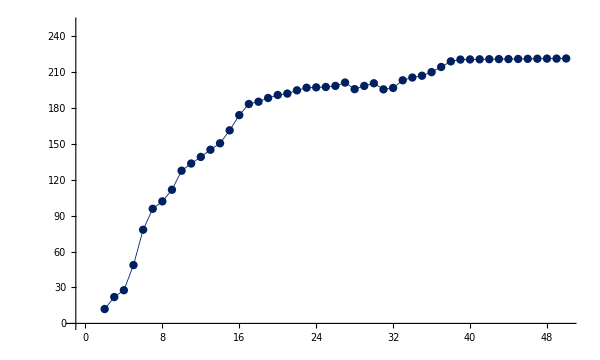

```mathematica
thickval=0.001;grawtr1=Show[Graphics[{colsea,Thickness[thickval],Line[data["water"]]}],Graphics[{colsea,PointSize[.01],Point[data["water"]]}],Axes->True,AxesOrigin->{-1,0},PlotRange->{{-1,50},{0,250}},Ticks->{Table[{i-1,Rotate[ToString[datatemp⟦i,2⟧], 60 Degree]},{i,2,Length[datatemp],7}]},TicksStyle->Directive["Times",12],AspectRatio->.6,ImageSize->600]
```

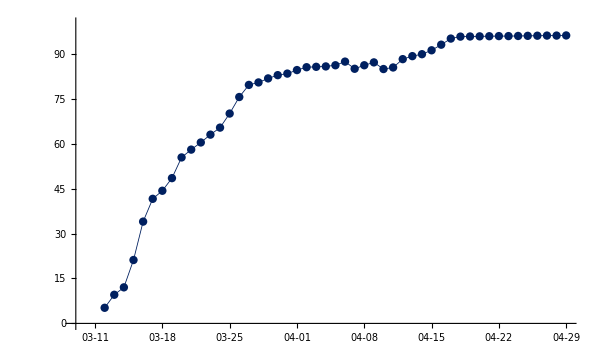

```mathematica
thickval=0.001;grawtr2=Show[Graphics[{colsea,Thickness[thickval],Line[Table[{data["water"]⟦i,1⟧,(data["water"]⟦i,2⟧)/230.*100.},{i,Length[data["water"]]}]]}],Graphics[{colsea,PointSize[.01],Point[Table[{data["water"]⟦i,1⟧,(data["water"]⟦i,2⟧)/230.*100.},{i,Length[data["water"]]}]]}],Axes->True,AxesOrigin->{-1,0},PlotRange->{{-1,50},{0,100}},Ticks->{Table[{i-1,Rotate[ToString[datatemp⟦i,2⟧], 60 Degree]},{i,2,Length[datatemp],7}], Automatic},TicksStyle->Directive["Times",12],AspectRatio->.6,ImageSize->600]
```

```mathematica
h[t_,a_,b_,c_]:=a*t*Exp[-(1/c)*(t/b)^c];
```

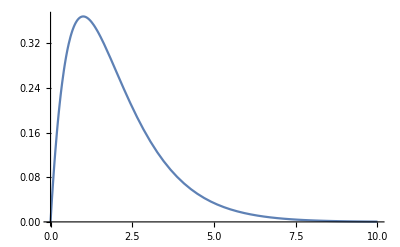

```mathematica
Plot[h[t,1,1,1],{t,0,10}]
```

```mathematica
S[t_,a_,b_,c_]:=Exp[-1*NIntegrate[h[τ,a,b,c],{τ,0,t}]];
```

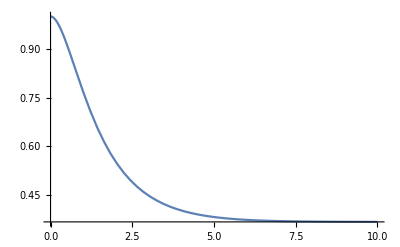

```mathematica
Plot[S[t,1,1,1],{t,0,10},PlotRange->All]
```

```mathematica
F[t_,a_,b_,c_]:=1-S[t,a,b,c];
```

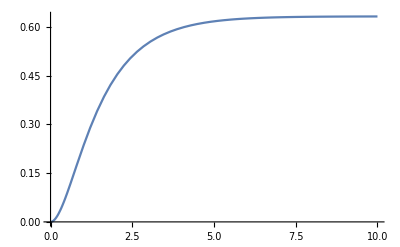

```mathematica
Plot[F[t,1,1,1],{t,0,10},PlotRange->All]
```

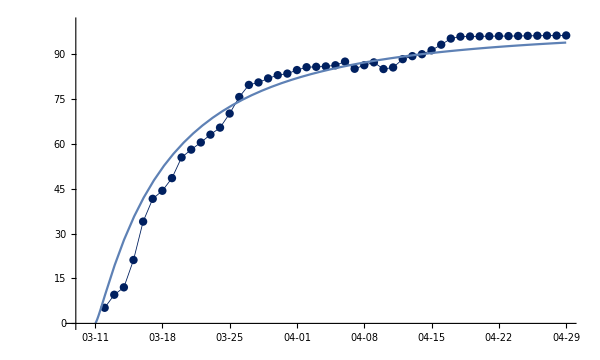

```mathematica
test2=Plot[100*F[t-1,13.2038,1.5676590017096623,0.1931346898281414],{t,0,50},PlotRange->All];
grawtr3F=Show[grawtr2,test2]
```

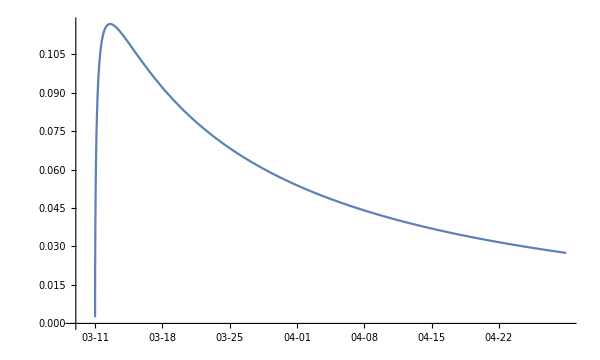

```mathematica
grawtr3h=Plot[h[t-1,13.2038,1.5676590017096623,0.1931346898281414],{t,0,50},Axes->True,AxesOrigin->{-1,0},PlotRange->{{-1,50},Automatic},Ticks->{Table[{i-1,Rotate[ToString[datatemp⟦i,2⟧], 60 Degree]},{i,2,50,7}], Automatic},TicksStyle->Directive["Times",12],AspectRatio->.6,ImageSize->600]
```

```mathematica
FindMaximum[h[t,13.2038,1.5676590017096623,0.1931346898281414],t]
```

{0.116759,{t→1.56766}}

```mathematica
Export["figure_water_a.png",grawtr3F,"PNG"];
Export["figure_water_b.png",grawtr3h,"PNG"];
```